# Librería para semigrupos numéricos

## Función de pertenencia

Indica si x pertenece o no al semigrupo generado por una lista de elementos s. Esta función va restando cada uno de los generadores. Devuelve verdadero si tras alguna recta nos da 0, y si al realizar otra operación, obtenemos un número negativo devolvemos falso.

```mathematica
pertenece[0, _] := True
 
pertenece[x_, {y_}] := Mod[x, y] == 0

pertenece[x_ /; x > 0, {y_, z__}] := pertenece[x, {z}] ||pertenece[x - y, {y, z}]
 
pertenece[x_, _] := False /; x < 0
```

#### Ejemplos:

```mathematica
pertenece[37,{5,6,9}]
```

True

```mathematica
pertenece[5,{4,7}]
```

False

## Función expresiones

Determina las expresiones de x en función de los elementos de la lista s.
Necesitamos las funciones auxiliares quitarepetidos y sumaei.
La función expresiones, restando los generadores creamos un árbol en el que apareceran las distintas expresiones del elemento en función de sus generadores.

```mathematica
quitarepetidos[{x___, y_, z___, y_, t___}] := quitarepetidos[{x, y, z, t}]
quitarepetidos[L_] := L
```

```mathematica
sumaei[i_, x_] := ReplacePart[x, x[[i]] + 1, i]
```

```mathematica
expresiones[x_ /; x > 0, s_] := 
Module[{expr, l}, 
l = Length[s]; 
expr = {}; 
           Do[If[x - s[[i]] >= 0, 
expr = Union[expr, (sumaei[i, #1] & ) /@ 
                            expresiones[x - s[[i]], s]]]; , {i, 1, l}]; 
quitarepetidos[expr]]
 
expresiones[x_ /; x < 0, _] := {}
 
expresiones[0, s_] := {Table[0, {Length[s]}]}
```

#### Ejemplos:

```mathematica
expresiones[37,{5,6,9}]
```

{{2,0,3},{2,3,1},{5,2,0}}

```mathematica
expresiones[37,{5,6,9}]
```

{{2,0,3},{2,3,1},{5,2,0}}

Podemos ver que sucede si un elemento no pertenece al semigrupo

```mathematica
expresiones[7,{5,6}]
```

{}

## Función Semigrupo

Muestra una lista con los elementos del semigrupo hasta que se completa su conjunto de Apéry respecto de la multiplicidad. El mcd({s}) tiene que ser 1\n , semigrupo[cond_funcionbooleana] muestra una lista con los elementos del semigrupo determinado por la condición cond  “.
Necesitamos las funciones auxiliares.

```mathematica
en[x_, y_] := Position[y, x] != {}
```

```mathematica
semiaux[cond_] :=
Module[
	{x, s, ap, r, m}, 
	x = 1;
	While[Not[cond[x]],x++];
	m=x;
	ap = Join[{m}, Table[0, {m - 1}]];
	x++;
	s={0,m};
	While[en[0, ap],
		(
			r = Mod[x, m] + 1; 
			If[cond[x], s=Join[s, {x}];
			If[ap[[r]]==0,ap[[r]] = x]];
		x++;
		)
	];
	If[m==1,{0,1},s]
]
(* pinta un semigrupo dado por una condicion, hasta que se completa el apery *)
```

```mathematica
semigrupo[cond_] := semiaux[cond]
```

```mathematica
semigrupo[{x__Integer}]:=semiaux[  pertenece[#,{x}] & ] /; GCD[x]==1
```

#### Ejemplos:

Calculamos el semigrupo generado por {5,7}

```mathematica
semigrupo[{5,7}]
```

{0,5,7,10,12,14,15,17,19,20,21,22,24,25,26,27,28}

Semigrupo formado por todos los mayores o iguales que 5

```mathematica
semigrupo[(#≥5)&]
```

{0,5,6,7,8,9}

Semigrupo numéricos formado por los números naturales que verifican que 7x mod 10 es menor o igual que x

```mathematica
semigrupo[(Mod[7#,10]≤#)&]
```

{0,3,5,6,8,9,10}

Semigrupo generado por {5,11,13}

```mathematica
semigrupo[ pertenece[#,{5,11,13}]  &]
```

{0,5,10,11,13,15,16,18,20,21,22,23,24}

## Función Apery

Calcula el conjunto de Apéry de x en el semigrupo generado por {s}  siempre que x pertenezca a {s} y mcd ({s})= 1
apery [{s_Intenger}] calcula el conjunto de apery respecto de la multiplicidad.
apery[x_Integer,cond_funcionbooleana] hace lo mismo pero con el semigrupo determinado por cond
Necesitamos la función auxiliar aperyaux y la función pertenece:

```mathematica
(* funcion auxiliar para el conjunto de apery *)

aperyaux[y_,gen:{m_, l__}] :=
  Module[{x, s, ap, r}, 
	x = Min[m,l]; s = {0};
           ap = Join[{y}, Table[0, {y - 1}]];
           While[en[0, ap],
                (r = Mod[x, y] + 1; 
                If[ap[[r]] != 0, 
		s = Join[s, {x}],
                       If[(Or @@ (en[#1, s] & ) /@ (x - gen)),
			(s = Join[s, {x}]; ap[[r]] = x;)
		]
	    ];
                x++;)
	]; 
     ap
]

(* pinta el conjunto de apery de un elemento en el semigrupo dado *)
```

```mathematica
apery[x_Integer,{y__Integer}]:=ReplacePart[aperyaux[x,{y}],0,1]/; pertenece[x,{y}] && GCD[y]==1

apery[{y__Integer}]:=apery[First[Sort[{y}]],{y}]

(* funcion auxiliar para el conjunto de apery *)

aperyaux[y_,cond_] :=
  Module[{x, ap, r}, x = 1; 
    ap = Join[{y}, Table[0, {y - 1}]];
    While[en[0, ap],
     (r = Mod[x, y] + 1;
      If[ap[[r]]==0 && cond[x],
	ap[[r]]=x];  
      x++;)
   ]; 
ap]

(* pinta el conjunto de apery de un elemento en el semigrupo dado *)
```

```mathematica
apery[x_Integer,cond_]:=ReplacePart[aperyaux[x,cond],0,1]/; cond[x]
```

#### Ejemplos:

Calculamos el Apery de 12 en el semigrupo {5,7 }

Claramente 12 pertenece a {5,7} pues 12=5+7

```mathematica
apery[12,{5,7}]
```

{0,25,14,15,28,5,30,7,20,21,10,35}

Vemos que 25-12 no está en el semigrupo generado por {5,7}

```mathematica
pertenece[25-12,{5,7}]
```

False

Calculamos el Apery de 9 en el semigrupo definido por la condición apery[9,(Mod[7 #, 10] ≤ #) &

Primero vemos que 9 pertenece al semigrupo

```mathematica
(Mod[7 #, 10] ≤ #) &[9]
```

True

```mathematica
apery[9,(Mod[7 #, 10] ≤ #) &]
```

{0,10,11,3,13,5,6,16,8}

Calculamos el Apery de 3 en el mismo semigrupo

Primero vemos que 3 pertenece al semigrupo

```mathematica
(Mod[7 #, 10] ≤ #) &[3]
```

True

```mathematica
apery[3,(Mod[7 #, 10] ≤ #) &]
```

{0,10,5}

## Función Pintaapery

Funcion que se apoya en apery[x, s] y pinta el diagrama de Hasse asociado al orden definido por el semigrupo

pintaapery[{s_Integer}] hace lo mismo, pero respecto de la multiplicidad.

Pinta el diagrama de Hasse asociado al conjunto de apery respecto  del orden inducido por el semigrupo .

Necesita la función auxiliar pertenece.

```mathematica
<<DiscreteMath`Combinatorica`
```

General::newpkg: DiscreteMath`Combinatorica` is now available as the Combinatorica Package. See the Compatibility Guide for updating information.

```mathematica
pintaapery[n_Integer, s_] :=With[{ap=apery[n,s]}, 
    ShowLabeledGraph[
    HasseDiagram[MakeGraph[ap, pertenece[#2 - #1, s] &]], 
    DisplayForm[RowBox[{#,Mod[#,n]}]]&/@ap]]
```

```mathematica
pintaapery[{s__Integer}]:=pintaapery[First[Sort[{s}]],{s}]
```

#### Ejemplos:

Recordamos quien es el Apery de 12 en {5,7}

```mathematica
apery[12, {5, 7}]
```

{0,25,14,15,28,5,30,7,20,21,10,35}

Pintamos el Apery de 12

Se puede observar que en el grafo aparece el elemento a la izquierda y el elemento módulo 12 a la derecha

Los elementos del grafo además están ordenados respecto al orden del semigrupo, así por ejemplo 28 solamente aparece por debajo del 35 pues 28+7=35 y en cambio 30-28=2 no está en el semigrupo {5,7}

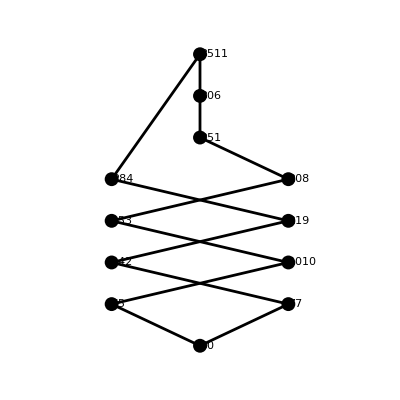

```mathematica
pintaapery[12,{5,7}]
```

## Función Frobenius

Calcula el número de Frobenius del semigrupo generado por {s}, siempre que éste sea un semigrupo numérico.
 Necesita la función auxiliar apery.

```mathematica
frobenius[{m_Integer,x__Integer}]:=Max[apery[m,{m,x}]]-m /; GCD[m,x]==1
```

#### Ejemplos:

Vemos ahora como puede usarse esta función

```mathematica
frobenius[{5,7}]
```

23

```mathematica
frobenius[{10,13,17}]
```

58

```mathematica
frobenius[{15,21,23,25}]
```

79

## Función Pseudofrobenius

Calcula el conjunto de pseudonúmeros de Frobenius del semigrupo generado por {s}, si éste semigrupo es numérico.
Necesita la función auxiliar apery.

```mathematica
pseudofrobenius[{m_Integer,x__Integer}]:=With[{ap=apery[m,{m,x}]}, Select[ap,
(And@@(Or[Not[en[#,ap]],#==0]&/@(ap-#)))&]-m] /; GCD[m,x]==1
```

#### Ejemplos:

```mathematica
pseudofrobenius[{10,13,17}]
```

{55,58}

El número de frobenius siempre ha de estar

```mathematica
frobenius[{10,13,17}]
```

58

## Función EH

Calcula el conjunto de pseudo números de Frobenius especiales del semigrupo generado por {s}, si este semigrupo es numérico.
Necesita las funciones auxiliares pseudofrobenius y pertenece.

```mathematica
EH[{s__Integer}]:=Select[pseudofrobenius[{s}],pertenece[2*#,{s}]&]
```

#### Ejemplos:

```mathematica
EH[{5,7,9}]
```

{11,13}

Vemos que en este caso coincide con el conjunto de pseudo números de frobenius

```mathematica
pseudofrobenius[{5,7,9}]
```

{11,13}

## Función H

Calcula el con junto de huecos del semigrupo generado por { s} ,si esté semigrupo es numérico.
Necesita las funciones auxiliares frobenius y semigrupo

```mathematica
H[s_] := With[{g = frobenius[s]}, Complement[Range[0, g], semigrupo[s]]]
```

#### Ejemplos:

Calculamos los huecos del semigrupo generado por {5,7,9}

```mathematica
H[{5,7,9}]
```

{1,2,3,4,6,8,11,13}

Claramente su número de frobenius ha de coincidir con el mayor de sus huecos

```mathematica
frobenius[{5,7,9}]
```

13

```mathematica
semigrupo[{5,7,9}]
```

{0,5,7,9,10,12,14,15,16,17,18}

## Función FH

Calcula el conjunto de huecos fundamentales del semigrupo generado por {s}, si éste semigrupo es numérico.

```mathematica
FH[s_] := 
  With[{h = H[s]}, 
    Select[h, (Not[MemberQ[h, 2 #]] && Not[MemberQ[h, 3 #]]) &]]
```

#### Ejemplos:

```mathematica
FH[{5,7,9}]
```

{6,8,11,13}

## Función FHM

Calcula el conjunto de huecos fundamentales respecto de la multiplicidad del semigrupo generado por {s}, si éste semigrupo es numérico

```mathematica
FHM[s_] := With[
		{h = H[s], m = Min[Select[s, # > 0 &]]}, 
                       Select[h, (Not[MemberQ[h, 2 #]] && Not[MemberQ[h, 3 #]] && 
                            Not[MemberQ[h, m + #]]) &
	            ]
	      ]
```

#### Ejemplos:

```mathematica
FHM[{5,7,9}]
```

{11,13}

## Función Grafo

Calcula el grafo asociado al elemento n respecto del semigrupo generado por {s}.

```mathematica
grafo[n_,s_]:={
	Select[s,(pertenece[n-#,s])&], 
	Select[Flatten[Outer[List,s,s],1],
	(And[pertenece[n-(Apply[Plus,#]),s],Apply[Less,#]])&]
}
```

#### Ejemplos:

```mathematica
semigrupo[{5, 7, 9}]
```

{0,5,7,9,10,12,14,15,16,17,18}

```mathematica
grafo[12,{5,7,9}]
```

{{5,7},{{5,7}}}

```mathematica
semigrupo[{3,5,7}]
```

{0,3,5,6,7}

```mathematica
grafo[10,{3,5,7}]
```

{{3,5,7},{{3,7}}}

```mathematica
grafo[12, {3, 5, 7}]
```

{{3,5,7},{{5,7}}}

```mathematica
grafo[14, {3, 5, 7}]
```

{{3,5,7},{{3,5}}}

```mathematica
grafo[11, {3, 5, 7}]
```

{{3,5},{{3,5}}}

## Función Componentes Conexas

Calcula las componentes conexas del grafo no dirigido con vértices {v} y lados {l}.
Necesitas las funciones auxiliares:

```mathematica
componentesconexasaux[{xx___,{x___,a_,y___},yy___,{u___,a_,v___},zz___}]:=
     componentesconexasaux[{xx,{x,a,y,u,v},yy,zz}]
componentesconexasaux[L_]:=L
```

```mathematica
componentesconexas[{{v__},{l___}}]:=componentesconexasaux[{Sequence@@(List/@ {v}),l}]
```

Calcula los relatores del semigrupo generado por {s}, si éste es un semigrupo numérico y da como salida los una lista de la forma {..., {n,G_n}, ...} con n elemento de <s> cuyo grafo es no conexo y G_n
las componentes conexas de ese grafo \n relatores[{s},True] pinta además los grafos no conexos de ese semigrupo .
Necesita de la función auxiliar:

```mathematica
relatoresaux[{x_,s_}]:=
	Module[{l},
            l=Length[s];
            If[l>1,Do[
                     Print[ pintaexpr[First[expresiones[x,s[[1]]]], s[[1]]] , " = ",
                     pintaexpr[First[expresiones[x,s[[i]]]], s[[i]]]],
                     {i,2,l}
		]
	]
  ]
```

```mathematica
relatoresprincipal[gen:{m_,s__},pinta_]:=
    Module[{ap,candidatos},
      ap=apery[m,gen];
      candidatos=quitarepetidos[Flatten[Outer[Plus,ap,gen],1]];
      candidatos=Map[{#,componentesconexas[grafo[#,gen]]}&,candidatos];
      candidatos=Select[candidatos,(Length[First[Rest[#]]]-1!=0)&];
      (*{Plus@@((Length[First[Rest[#]]]-1)&/@candidatos), candidatos}*)
          Print["N. relatores ", Plus@@((Length[First[Rest[#]]]-1)&/@candidatos)];
      Map[relatoresaux[#]&,candidatos];
          If[pinta,Map[pintagrafo[First[#],gen]&,candidatos]];
          candidatos
    ]/;GCD[m,s]==1
             
relatores[gen_,pinta_:False]:=relatoresprincipal[gen,pinta]
```

#### Ejemplos:

```mathematica
relatores[{5,7,9},True]
```

N. relatores 3

pintaexpr[{5},{5}] = pintaexpr[{1,2},{7,9}]

pintaexpr[{1,1},{5,9}] = pintaexpr[{2},{7}]

pintaexpr[{4,1},{5,7}] = pintaexpr[{3},{9}]

```mathematica
{{25,{{5},{7,9}}},{14,{{5,9},{7}}},{27,{{5,7},{9}}}}
```

El sistema de generadores de la congruencia sería en este caso {((5,0,0),(0,1,2)),((1,0,1),(0,2,0)),((4,1,0),(0,0,3))}

```mathematica
relatores[{3,5,7},True]
```

N. relatores 3

pintaexpr[{1,1},{3,7}] = pintaexpr[{2},{5}]

pintaexpr[{4},{3}] = pintaexpr[{1,1},{5,7}]

pintaexpr[{3,1},{3,5}] = pintaexpr[{2},{7}]

{{10,{{3,7},{5}}},{12,{{3},{5,7}}},{14,{{3,5},{7}}}}

El sistema de generadores de la congruencia sería en este caso {((1,0,1),(0,2,0)),((4,0,0),(0,1,1)),((3,1,0),(0,0,2))}

## Función Sistemaminimal

Devuelve el sistema minimal de generadores del semigrupo generado por {s}, sistemaminimal[cond],  da el sistema minimal de generadores del semigrupo determinado por la condición “cond”. 
Necesita de las funciones auxiliares apery y pertenece.

```mathematica
sistemaminimal[{y__Integer}]:=Module[{x},x=Select[{y},(#!=0)&];
  If[x=={},Return[{}]];
  If[GCD@@x==1, sistemaminimal2[x],sistemaminimal1[x]]]

sistemaminimal1[{x___Integer, y_Integer, z___Integer}] := sistemaminimal1[{x,
 z}] /;pertenece[y, {x, z}] 

sistemaminimal1[{x__Integer}] := {x} //Sort

sistemaminimal2[{x__Integer}]:=Module[{m,ap}, m=Min[x]; ap=apery[m,{x}]/. 0->m;
  Select[ap, (And@@(Or[Not[en[#,ap]],#==0]&/@(#-ap)))&]] // Sort
```

```mathematica
sistemaminimal[cond_]:=Module[{m},
  m=1; 
  If[cond[m]===True,Return[{1}]];
  If[cond[m]===False,
  While[Not[cond[m]],m++];
  sistemaminimal[Join[{m},Drop[apery[m,cond],1]]],Print[cond," no parece ser una condición"]]
  (*sistemaminimal[Join[{m},Drop[apery[m,cond],1]]]*)
  ] // Sort
```

#### Ejemplos:

Veamos quien es el sistema minimal de generadores de {5,7,9,12,15,17}

Claramente 12=5+7 por lo que ha de ser eliminado

```mathematica
sistemaminimal[{5,7,9,12,15,17}]
```

{5,7,9}

Ejemplo con condiciones

```mathematica
sistemaminimal[(Mod[8 #, 17] ≤ #) &]
```

{7,9,11,12,13,15,17}

## Función Quitaelemento

Calcula un sistema minimal de generadores de <s>\{n}.

```mathematica
quitaelemento[n_Integer,{m_Integer,s__Integer}]:=
With[{ap=(apery[m,{m,s}]/. 0->m)}, sistemaminimal[(ap/. n->(n+m))]]/; n!=m

quitaelemento[n_Integer,{n_Integer,m_Integer,s___Integer}]:= 
 With[{ap=(apery[m,{n,m,s}]/. 0->m)}, 
	sistemaminimal[(ap/. n->n+m)]]
```

#### Ejemplos:

Vemos quien genera el semigrupo que se obtiene al quitar el 7 del semigrupo generado por {5,7}

```mathematica
quitaelemento[7,{5,7}]
```

{5,12,14,21}

Vemos quien genera el semigrupo que se obtiene al quitar el 5 del semigrupo generado por {5,7}

```mathematica
quitaelemento[5, {5, 7}]
```

{7,10,12,15}

## Función Ponelemento

Calcula un sistema minimal de generadores de <s,n>.

```mathematica
ponelemento[n_Integer,{s__Integer}]:=sistemaminimal[{n,s}]
```

#### Ejemplos:

Calculamos el semigrupo numérico que se obtiene de añadir al semigrupo generado por {10,13,21} el 7

Vemos que el 7 es un hueco del semigrupo

```mathematica
H[{10, 13, 21}]
```

{1,2,3,4,5,6,7,8,9,11,12,14,15,16,17,18,19,22,24,25,27,28,29,32,35,37,38,45,48,58}

```mathematica
ponelemento[7,{10,13,21}]
```

{7,10,13}

## Función Irreducibles

Da una lista con los semigrupos irreducibles con número de Frobenius n.
Necesitamos las funciones auxiliares:

```mathematica
unsemigrupoirreducible[n_Integer, {}] := 
	Module[{k}, 
		k = 1; While[Mod[n, k] ==0, k++]; 
		unsemigrupoirreducible[n, {k}]
]

unsemigrupoirreducible[n_Integer, {s__Integer}] := 
	Module[{k}, 
		k = Last[{s}] +1; 
		While[pertenece[k, {s}] || pertenece[n, {s, k}], If[k>n+First[{s}],
                       Return[{s}]]; k++;]; 
		unsemigrupoirreducible[n, {s, k}]]

unsemigrupoirreducible[n_Integer]:=unsemigrupoirreducible[n,{}]
```

```mathematica
hijosirred[{s__}, g_] := Module[{l}, l = candidatosirred[{s}, g]; 
      (ponelemento[g - #1, quitaelemento[#1, {s}]] & ) /@ l ]

candidatosirred[{s__}, g_] := Select[{s}, 
     Position[EH[quitaelemento[#1, {s}]], g - #1] != {} & ]
```

```mathematica
irreducibles[g_Integer] := Module[{A, B, s}, s = unsemigrupoirreducible[g]; A
      = {s}; B = hijosirred[s, g]; While[B != {}, s = First[B]; B = Rest[B];
      If[Position[A, s] == {}, A = Union[A, {s}]; Print[s]; B = Union[B,
      hijosirred[s, g]]]]; A]
```

#### Ejemplos:

Semigrupo irreducibles con número de frobenius igual a 5

```mathematica
irreducibles[5]
```

{3,4}

{{2,7},{3,4}}

Semigrupo irreducibles con número de frobenius igual a 17

```mathematica
irreducibles[17]
```

{4,6,15}

{4,10,11}

{4,7}

{6,8,10,13,15}

{6,7,8}

{6,7,9}

{6,9,10,13,14}

{3,10}

{7,8,11,12,13}

{7,9,11,12,13,15}

{8,10,11,12,13,14,15}

{5,8,11,14}

{5,9,11,13}

{9,10,11,12,13,14,15,16}

{{2,19},{3,10},{4,7},{4,6,15},{4,10,11},{6,7,8},{6,7,9},{5,8,11,14},{5,9,11,13},{6,8,10,13,15},{6,9,10,13,14},{7,8,11,12,13},{7,9,11,12,13,15},{8,10,11,12,13,14,15},{9,10,11,12,13,14,15,16}}

Semigrupo irreducibles con número de frobenius igual a 18

```mathematica
irreducibles[18]
```

{8,11,12,13,14,15,17}

{7,8,12,13,17}

{7,10,12,13,15,16}

{5,7,16}

{5,11,12,14}

{10,11,12,13,14,15,16,17,19}

{{4,11,13},{5,7,16},{5,11,12,14},{7,8,12,13,17},{7,10,12,13,15,16},{8,11,12,13,14,15,17},{10,11,12,13,14,15,16,17,19}}

Semigrupo irreducibles con número de frobenius igual a 19

```mathematica
irreducibles[19]
```

{4,6,17}

{4,10,13}

{4,9,14}

{6,8,10,15,17}

{6,8,9}

{6,9,11,14,16}

{3,11}

{6,10,11,14,15}

{5,6}

{5,11,12,13}

{5,8,12}

{8,9,12,13,14,15}

{7,8,9,13}

{7,8,10,13}

{7,9,11,13,15,17}

{7,10,11,13,15,16}

{8,10,12,13,14,15,17}

{9,11,12,13,14,15,16,17}

{10,11,12,13,14,15,16,17,18}

{{2,21},{3,11},{5,6},{4,6,17},{4,9,14},{4,10,13},{5,8,12},{6,8,9},{5,11,12,13},{7,8,9,13},{7,8,10,13},{6,8,10,15,17},{6,9,11,14,16},{6,10,11,14,15},{7,9,11,13,15,17},{7,10,11,13,15,16},{8,9,12,13,14,15},{8,10,12,13,14,15,17},{9,11,12,13,14,15,16,17},{10,11,12,13,14,15,16,17,18}}

```mathematica
frobenius[{4,9,14}]
```

19

```mathematica
H[{4,9,14}]
```

{1,2,3,5,6,7,10,11,15,19}

Todo semigrupo S irreducible verifica que si x+y es igual al número de frobenius entonces x o y han de pertenecer a S (sólo uno de ellos)

En el ejemplo anterior tenemos que 19=18+1, 19=17+2, 19=10+9. Si nos fijamos tenemos que

```mathematica
{pertenece[18,{4,9,14}],pertenece[1,{4,9,14}]}
```

{True,False}

```mathematica
{pertenece[17,{4,9,14}],pertenece[2,{4,9,14}]}
```

{True,False}

```mathematica
{pertenece[16,{4,9,14}],pertenece[3,{4,9,14}]}
```

{True,False}

```mathematica
{pertenece[15,{4,9,14}],pertenece[4,{4,9,14}]}
```

{False,True}

```mathematica
{pertenece[14,{4,9,14}],pertenece[5,{4,9,14}]}
```

{True,False}

```mathematica
{pertenece[13,{4,9,14}],pertenece[6,{4,9,14}]}
```

{True,False}

```mathematica
{pertenece[12,{4,9,14}],pertenece[7,{4,9,14}]}
```

{True,False}

```mathematica
{pertenece[11,{4,9,14}],pertenece[8,{4,9,14}]}
```

{False,True}

```mathematica
{pertenece[10,{4,9,14}],pertenece[9,{4,9,14}]}
```

{False,True}

## Función Irreducible

Busca un irreducible con número de Frobenius g y dimensión de inmersión (número de generadores minimales) menor o igual que e.

```mathematica
irreducible[g_Integer,e_Integer]:= Module[{A, B, s}, s =
      unsemigrupoirreducible[g]; A = {s}; B = hijosirred[s, g]; While[B != {},
      s = First[B]; If[Length[s]<=e,Return[s]];
      B = Rest[B]; If[Position[A, s] == {}, A = Union[A, {s}]; B
      = Union[B, hijosirred[s, g]]]]; A]
```

#### Ejemplos

Semigrupo irreducibles con número de frobenius igual a 17 y dimensión de inmersión menor o igual que 5

```mathematica
irreducible[17,5]
```

{4,6,15}